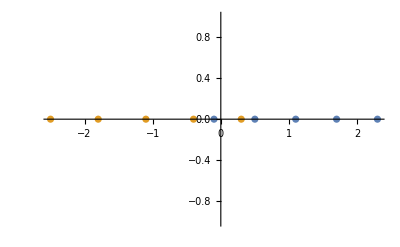

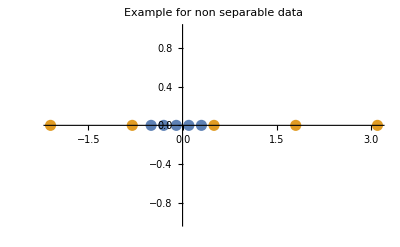

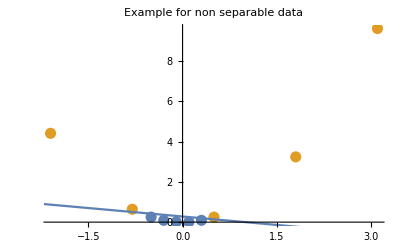

```mathematica
points1Seperable=Table[{0.6*i-0.2,0},{i,5}]; (*belongs on the right side *)
points2Seperable=Table[{-0.6*i+0.2,0},{i,5}]; (*belongs on the left side *)
points1=Table[{0.6*i-0.7,0},{i,5}];
points2=Table[{-0.7*i+1.0,0},{i,5}]; 
points1Quad=Table[{(0.2*i-0.7),(0.2*i-0.7)^2},{i,5}];
points1NonQuad=Table[{(0.2*i-0.7),0},{i,5}];
points2Quad=Table[{(-1.3*i+4.4),(-1.3*i+4.4)^2},{i,5}];
points2NonQuad=Table[{(-1.3*i+4.4),0},{i,5}];
ListPlot[{points1, points2}]
ListPlot[{points1NonQuad, points2NonQuad},PlotStyle->PointSize[0.02],PlotLabel->"Example for non separable data"]
Show[ListPlot[{points1Quad, points2Quad},PlotStyle->PointSize[0.02],PlotLabel->"Example for non separable data"],Plot[-0.28*x+0.28,{x,-5,5}]]
```

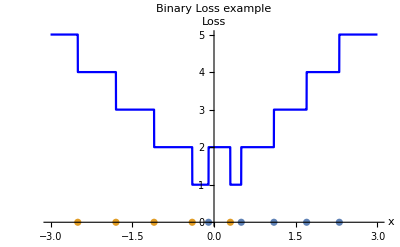

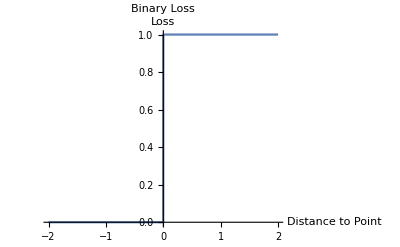

```mathematica
lossName="Binary Loss";
binLoss[x_,p_,class_]:=If[class==1,If[p>x,0,1],If[p<x,0,1]];
applyLossForPlt[x_,points_,class_,lossFKT_]:=Total[Map[Function[p,lossFKT[x,p[[1]],class]],points]];
Show[Plot[{applyLossForPlt[x,points1,1,binLoss]+applyLossForPlt[x,points2,2,binLoss],0},{x,-3,3},PlotStyle->{Blue,White}, Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2}]]
Plot[binLoss[x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

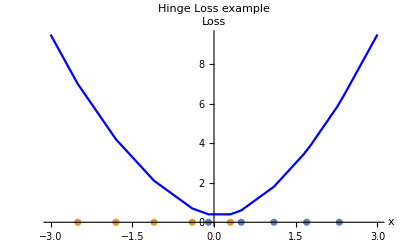

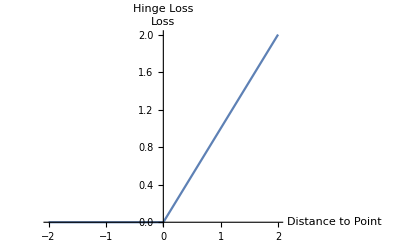

```mathematica
hingeLoss[x_,p_,class_]:=If[class==1,Max[0,x-p],Max[0,p-x]];
lossName="Hinge Loss";
Show[Plot[{applyLossForPlt[x,points1,1,hingeLoss]+applyLossForPlt[x,points2,2,hingeLoss],0},{x,-3,3},PlotStyle->{Blue,White}, Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2}]]
Plot[hingeLoss[x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

0.4

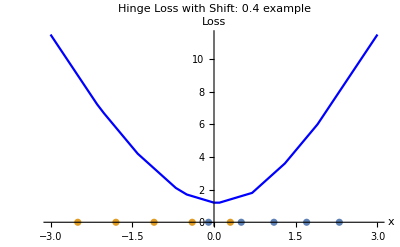

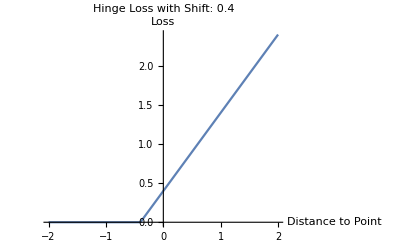

```mathematica
hingeLossShift[shift_]:=Function[{x,p,class},If[class==1,Max[0,x-p+shift],Max[0,p-x+shift]]];
sft=0.4
lossName="Hinge Loss with Shift: " <>ToString[sft];
Show[Plot[{applyLossForPlt[x,points1,1,hingeLossShift[sft]] + applyLossForPlt[x,points2,2,hingeLossShift[sft]],0},{x,-3,3},PlotStyle->{Blue,White},Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2}]]
Plot[hingeLossShift[sft][x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

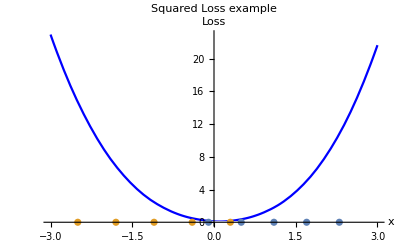

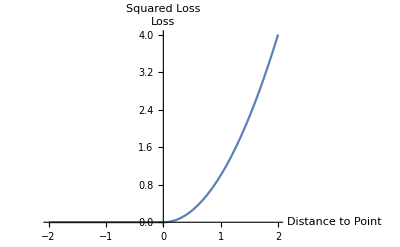

```mathematica
mseLoss[x_,p_,class_]:=If[class==1,(Max[0,x-p])^2,(Max[0,p-x])^2];
lossName="Squared Loss";
Show[Plot[{applyLossForPlt[x,points1,1,mseLoss]+applyLossForPlt[x,points2,2,mseLoss],0},{x,-3,3},PlotStyle->{Blue,White}, Exclusions->None, PlotLabel->lossName<>" example",AxesLabel->{x,Loss}],ListPlot[{points1, points2}]]
Plot[mseLoss[x,0,1],{x,-2,2},PlotLabel->lossName,AxesLabel->{"Distance to Point",Loss}]
```

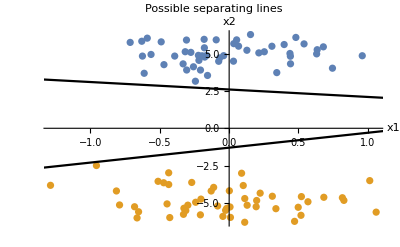

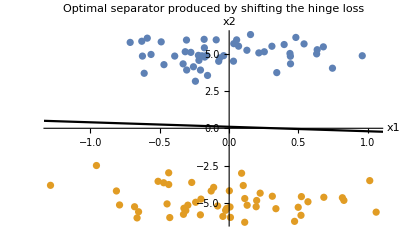

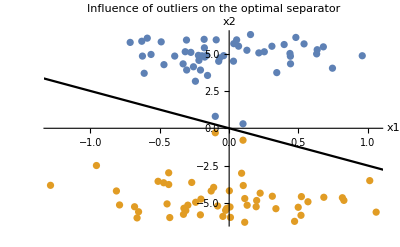

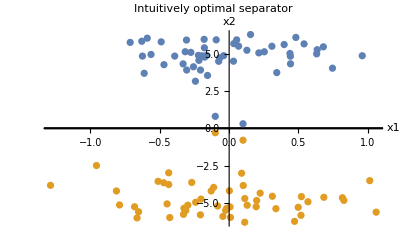

```mathematica
SeedRandom[45];
numsToGenerate=50;
spread = 0.4;
points1SVM=Table[{RandomVariate[NormalDistribution[0,spread]],RandomVariate[NormalDistribution[5.0,spread*2]]},{i,numsToGenerate}] ;(*belongs on the upper quadrant side *)
points2SVM=Table[{RandomVariate[NormalDistribution[0,spread]],RandomVariate[NormalDistribution[-5.0,spread*2]]},{i,numsToGenerate}] ;(*belongs on the lower quadrant side *)
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Possible separating lines",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{1.0*x-1.3,-0.5*x+2.6},{x,-3.5,3},Evaluated->True,PlotStyle->{Black,Black}]]
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Optimal separator produced by shifting the hinge loss",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{-0.3*x+0.1},{x,-3.5,3},Evaluated->True,PlotStyle->{Black}]]
outlieres1 = {{0.1,0.3},{-0.1,0.8}} ;
outlieres2 = {{-0.1,-0.3},{0.1,-0.8}};
Do[AppendTo[points1SVM,i],{i,outlieres1}];
Do[AppendTo[points2SVM,i],{i,outlieres2}];
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Influence of outliers on the optimal separator",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{-2.5*x+0.0},{x,-3.5,3},Evaluated->True,PlotStyle->{Black}]]
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Intuitively optimal separator",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{0},{x,-3.5,3},Evaluated->True,PlotStyle->{Black}]]
```

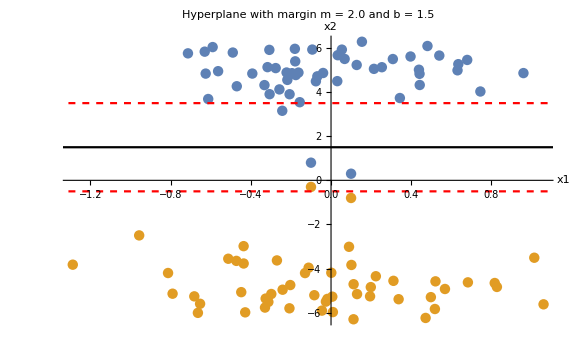

```mathematica
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Hyperplane with margin m = 2.0 and b = 1.5",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{1.5,3.5,-0.5},{x,-3.5,3},Evaluated->True,PlotStyle->{Black,{Red,Dashed},{Red,Dashed}}],ImageSize->Large]
```

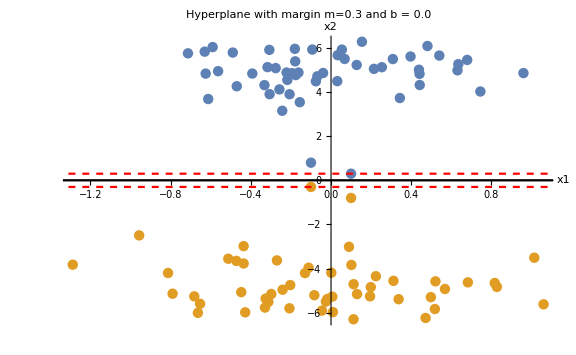

```mathematica
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Hyperplane with margin m=0.3 and b = 0.0",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{0.0,0.3,-0.3},{x,-3.5,3},Evaluated->True,PlotStyle->{Black,{Red,Dashed},{Red,Dashed}}],ImageSize->Large]
```

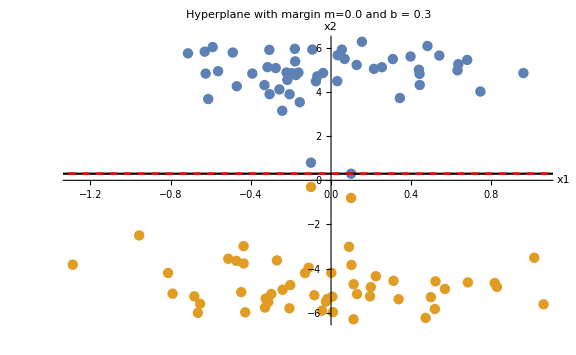

```mathematica
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Hyperplane with margin m=0.0 and b = 0.3",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{0.3,0.3,0.3},{x,-3.5,3},Evaluated->True,PlotStyle->{Black,{Red,Dashed},{Red,Dashed}}],ImageSize->Large]
```

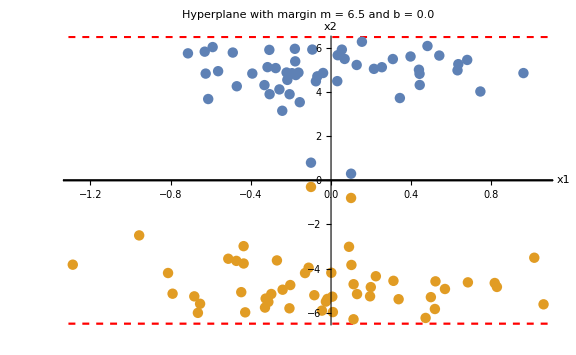

```mathematica
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Hyperplane with margin m = 6.5 and b = 0.0",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{0.0,6.5,-6.5},{x,-3.5,3},Evaluated->True,PlotStyle->{Black,{Red,Dashed},{Red,Dashed}}],ImageSize->Large]
```

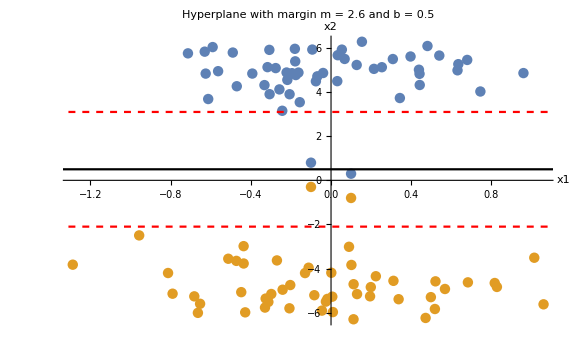

```mathematica
Show[ListPlot[{points1SVM,points2SVM},PlotRange->All,PlotLabel->"Hyperplane with margin m = 2.6 and b = 0.5",AxesLabel->{x1,x2},PlotStyle->PointSize[0.013]],Plot[{0.5,3.1,-2.1},{x,-3.5,3},Evaluated->True,PlotStyle->{Black,{Red,Dashed},{Red,Dashed}}],ImageSize->Large]
```

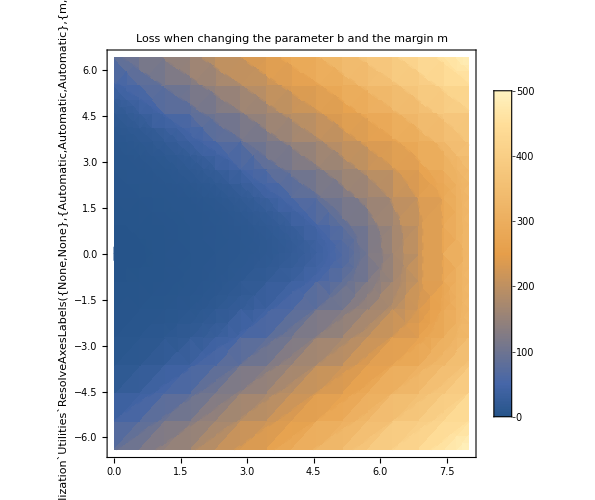

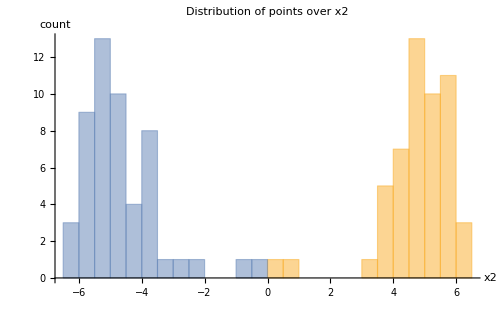

```mathematica
points1yProjection=Table[points1SVM[[i]][[2]],{i,Length[points1SVM]}];
points2yProjection=Table[points2SVM[[i]][[2]],{i,Length[points2SVM]}];
applyLossForSVMPlt[x_,points_,class_,lossFKT_]:=Total[Map[Function[p,lossFKT[x,p[[2]],class]],points]];
DensityPlot[applyLossForSVMPlt[y,points1SVM,1,hingeLossShift[sft]]+applyLossForSVMPlt[y,points2SVM,2,hingeLossShift[sft]],{sft,0,8},{y,-6.4,6.4},MeshFunctions->{#3&,#3&},Mesh->{10,{0}},MeshStyle->{Dashed,Black},PlotLabel->"Loss when changing the parameter b and the margin m",AxesLabel->{m,b},Exclusions->None,ImageSize->{500,500},PlotLegends->Placed[Automatic,Left],Exclusions->None]
Histogram[{points1yProjection,points2yProjection},20,AxesLabel->{x2,count},ImageSize->{500,300},PlotLabel->"Distribution of points over x2"]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum :: fmgz will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

General::stop: Further output of FindMinimum :: fmgz will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

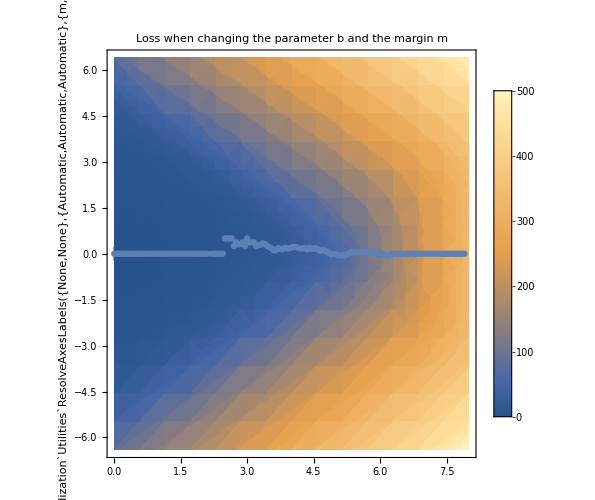

```mathematica
xAxis1=Range[0,8,0.05];
optimalBOverM=Table[{xAxis1[[IntegerPart[(sft+0.05)*20]]],FindMinimum[applyLossForSVMPlt[y,points1SVM,1,hingeLossShift[sft]]+applyLossForSVMPlt[y,points2SVM,2,hingeLossShift[sft]],{y,0}][[2]][[1]][[2]]},{sft,0,7.9,0.05}];
optimalLossOverM=Table[{xAxis1[[IntegerPart[(sft+0.05)*20]]],FindMinimum[applyLossForSVMPlt[y,points1SVM,1,hingeLossShift[sft]]+applyLossForSVMPlt[y,points2SVM,2,hingeLossShift[sft]],{y,0}][[1]]},{sft,0,7.9,0.05}];
Show[DensityPlot[applyLossForSVMPlt[y,points1SVM,1,hingeLossShift[sft]]+applyLossForSVMPlt[y,points2SVM,2,hingeLossShift[sft]],{sft,0,8},{y,-6.4,6.4},MeshFunctions->{#3&,#3&},Mesh->{10,{0}},MeshStyle->{Dashed,Black},PlotLabel->"Loss when changing the parameter b and the margin m",AxesLabel->{m,b},Exclusions->None,ImageSize->{500,500},PlotLegends->Placed[Automatic,Left],Exclusions->None],ListPlot[optimalBOverM]]
```

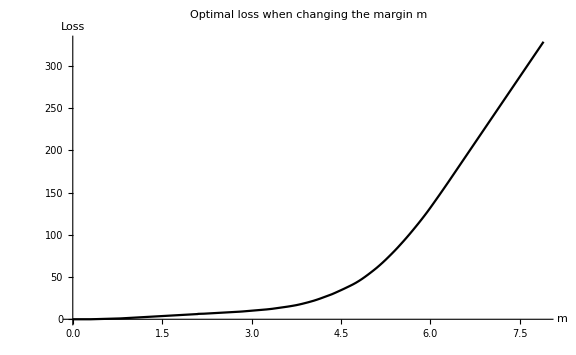

```mathematica
ListPlot[optimalLossOverM,Joined->True,AxesLabel->{m,Loss},PlotLabel->"Optimal loss when changing the margin m",ImageSize->Large, PlotStyle->{Black}]
```

Power::infy: Infinite expression 1/0. encountered.

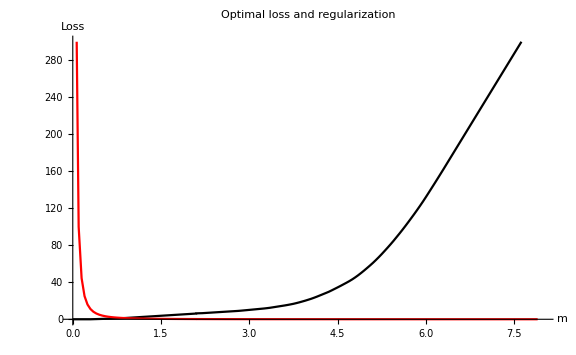

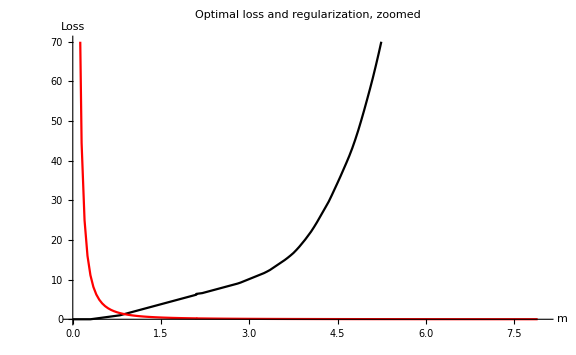

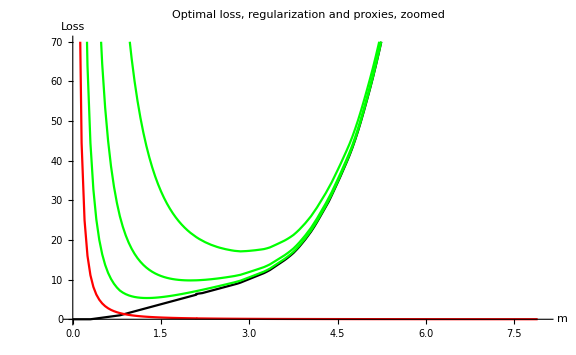

```mathematica
regressor=Table[{xAxis1[[IntegerPart[(x+0.05)*20]]],optimalLossOverM[[Length[optimalLossOverM]]][[2]]*0.5/(x+0.2)},{x,0,7.9,0.05}];
regressor=Table[{xAxis1[[IntegerPart[(m+0.05)*20]]],(1/m)^2},{m,0,7.9,0.05}];
prox1=Table[{xAxis1[[IntegerPart[(m+0.05)*20]]],optimalLossOverM[[IntegerPart[(m+0.05)*20]]][[2]]+regressor[[IntegerPart[(m+0.05)*20]]][[2]]*4},{m,0.05,7.9,0.05}];
prox2=Table[{xAxis1[[IntegerPart[(m+0.05)*20]]],optimalLossOverM[[IntegerPart[(m+0.05)*20]]][[2]]+regressor[[IntegerPart[(m+0.05)*20]]][[2]]*16},{m,0.05,7.9,0.05}];
prox3=Table[{xAxis1[[IntegerPart[(m+0.05)*20]]],optimalLossOverM[[IntegerPart[(m+0.05)*20]]][[2]]+regressor[[IntegerPart[(m+0.05)*20]]][[2]]*64},{m,0.05,7.9,0.05}];
ListPlot[{optimalLossOverM,regressor},Joined->True,AxesLabel->{m,Loss},PlotLabel->"Optimal loss and regularization",ImageSize->Large, PlotStyle->{Black,Red,Green,Green,Green},PlotRange->{{0,8},{0,300}}]
ListPlot[{optimalLossOverM,regressor},Joined->True,AxesLabel->{m,Loss},PlotLabel->"Optimal loss and regularization, zoomed",ImageSize->Large, PlotStyle->{Black,Red,Green,Green,Green},PlotRange->{{0,8},{0,70}}]
ListPlot[{optimalLossOverM,regressor,prox1,prox2,prox3},Joined->True,AxesLabel->{m,Loss},PlotLabel->"Optimal loss, regularization and proxies, zoomed",ImageSize->Large, PlotStyle->{Black,Red,Green,Green,Green},PlotRange->{{0,8},{0,70}}]
```